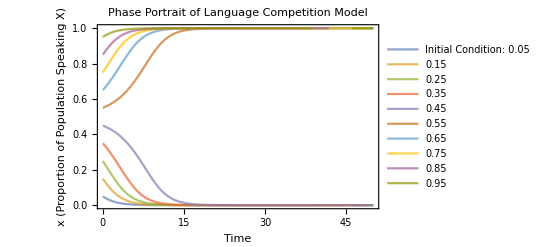

```mathematica
(*Define the equation for dx/dt*)
languageCompetitionModel[x_,s_,a_]:=s (1-x) x^a-(1-s) x (1-x)^a;

(*Defining the parameters*)
s=0.5;

(*Perceived status parameter*)
a=2;

(*Exponent parameter*)solutions=Table[NDSolve[{x'[t]==languageCompetitionModel[x[t],s,a],x[0]==x0},x[t],{t,0,50}],{x0,0.05,0.95,0.1}];

colors=ColorData[97,"ColorList"];

plot=Plot[Evaluate[x[t]/.solutions[[1]]],{t,0,50},PlotRange->{0,1},PlotStyle->{Directive[Opacity[0.7],colors[[1]]]},PlotLegends->{"Initial Condition: 0.05"}];

Do[plot=Show[plot,Plot[Evaluate[x[t]/.solutions[[i]]],{t,0,50},PlotRange->{0,1},PlotStyle->{Directive[Opacity[0.7],colors[[i]]]},PlotLegends->{ToString[0.05+(i-1)*0.1]}]],{i,2,Length[solutions]}];

(*Display the final plot with all the lines and legend*)
Show[plot,PlotRange->{0,1},Frame->True,FrameLabel->{"Time","x (Proportion of Population Speaking X)"},PlotLabel->"Phase Portrait of Language Competition Model"]
```